-1/(-2+x)

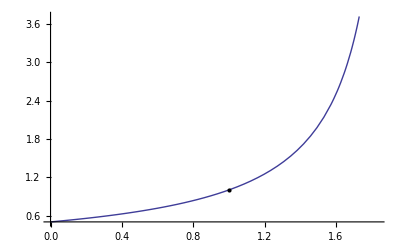

```mathematica
f[x_]=-1/(x-2)
A=Plot[f[x],{x,0,1.833}];
B=Graphics[Point[{1,1}]];
Show[A,B]
```

3.333/(2.-0.30003 x)

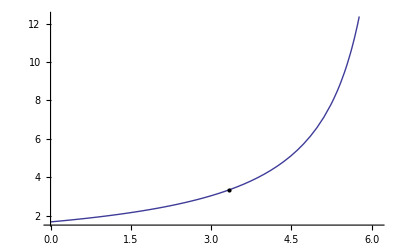

```mathematica
g[x_]=Simplify[3.333*f[x/3.333]]
A=Plot[g[x],{x,0,1.833*3.333}];
B=Graphics[Point[{3.333,3.333}]];
Show[A,B]
```

```mathematica
3.5-3.333
```

0.167

```mathematica
gg[x_]=Simplify[g[x-(3.5-3.333)]]
```

3.333/(2.05011-0.30003 x)

```mathematica
3-gg[3.5]
```

-0.333

11.1089/(2.-0.090018 x)

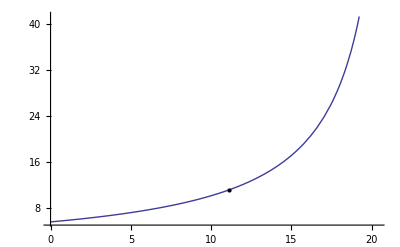

```mathematica
h[x_]=Simplify[3.333*g[x/3.333]]
A=Plot[h[x],{x,0,3.333^2*1.833}];
B=Graphics[Point[{3.333^2,3.333^2}]];
Show[A,B]
```

```mathematica
hh[x_]=Simplify[h[x-(6-3.333^2)]]
```

11.1089/(1.54011-0.090018 x)

```mathematica
3-hh[6]
```

-8.10889